```mathematica
ClearAll["Global`*"]
```

```mathematica
NotebookSave[];
```

```mathematica
SetDirectory[ NotebookDirectory[]]
```

/Users/stasya/prj/B-K

### Belle II parameters

```mathematica
Belle2params={γβB:>0.248,RKLM:>3,θKLMMin:>40 Degree, θKLMMax:>129 Degree,RCDC:>1.62,θCDCmin:>17 Degree, θCDCMax:>150 Degree};
```

### Init

```mathematica
tplus=(mB+mK)^2;
tminus=(mB-mK)^2;
tzero=tplus(1-Sqrt[1-tminus/tplus]);
```

```mathematica
z[t_]=(Sqrt[tplus-t]-Sqrt[tplus-tzero])/(Sqrt[tplus-t]+Sqrt[tplus-tzero]);
```

```mathematica
F[q.b2_,x_]=1/(1-(q.b2)/Subscript[m, R,x]^2)Sum[Subscript[α, k,x](z[q.b2]-z[0])^k,{k,0,2}]//Simplify;
```

```mathematica
formFactors={fplus[q.b2_]:> F[q.b2,fplus], fzero[q.b2_]:> F[q.b2,fzero]};
```

```mathematica
(* all masses (and mass-dimension quantities) in GeV units *)
```

```mathematica
constants = {GevToInverseSec :> 1.5 10^24};
values={Subscript[α, 0,fzero]:>0.329, Subscript[α, 1,fzero]:>0.195,Subscript[α, 2,fzero]:>-0.446,Subscript[α, 0,fplus]:>0.329,Subscript[α, 1,fplus]:>-0.876,Subscript[α, 2,fplus]:>0.006,Subscript[m, R,fzero]:>5.54 , Subscript[m, R,fplus]:>5.325 };
```

```mathematica
masses={MW:>80.38,mW:>80.38,MZ:>91.19,mZ:>91.19,MB:>4.18,mb:>4.18,MC:>1.28,mc:>1.28,MU:>0.0022,mu:>0.0022,MT:>173,mt:>173,MS:>0.095,ms:>0.095,mB:>5.279,mK:>0.4937,mπ:>0.14,mD:>1.86,v:>246,me:>0.000511,mμ:>0.106,mτ:>1.777,MD:>0.0047,md:>0.0047,Γh:>0.013,mBs:>5.367,fBs:>0.227,mBd:>5.280,fBd:>0.188,vev:>246.22};
ckms={CKM[3,3]:>0.999,Vtb:>0.999,CKM[3,2]:>0.0404,Vts:>0.0404,CKM[2,3]:>0.0412,Vcb:>0.0412,CKM[2,2]:>0.973,Vcs:>0.973, Vtd:> 8.1/1000};
couplings={EL:>Sqrt[4 π*7.297/1000],SW:>Sqrt[0.231],CW:>Sqrt[1-0.231],GF:>1.166*10^(-5),Subscript[α,em]:>7.297*10^-3,alphaem:>7.297*10^-3,alphas:>0.1181,Subscript[X,t]:>1.469,sw.b2:>0.231};
eulergamma={Subscript[γ,E]:>0.5772};
```

### Γϕ

```mathematica
datapointsππ=ReadList[File["rate_pipi.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

ReadList::noopen: Cannot open File[rate_pipi.dat].

```mathematica
datapointsππ={{0.28001323,5.17024*10^(-10)},{0.27784854,1.0525554*10^(-9)},{0.2877911,1.8218304*10^(-9)},{0.30592537,3.3623317*10^(-9)},{0.33365947,5.277515*10^(-9)},{0.3639078,8.283586*10^(-9)},{0.41079497,1.2181233*10^(-8)},{0.47179008,1.7907567*10^(-8)},{0.5560635,2.7178222*10^(-8)},{0.6442094,4.2615103*10^(-8)},{0.73974603,5.5053757*10^(-8)},{0.8280175,9.213942*10^(-8)},{0.8877805,1.6462049*10^(-7)},{0.9437583,3.1379568*10^(-7)},{0.97783643,7.033213*10^(-7)},{1.002676,3.6842826*10^(-7)},{1.036807,1.5896644*10^(-7)},{1.0629779,7.317836*10^(-8)},{1.108985,3.958082*10^(-8)},{1.1371115,2.0074902*10^(-8)},{1.1865596,1.27616815*10^(-8)},{1.2277195,9.23311*10^(-9)},{1.2817607,8.933028*10^(-9)},{1.3385478,1.08358424*10^(-8)},{1.3852515,9.2141486*10^(-9)},{1.47,4.38*10^(-9)},{1.5,2.5269602*10^(-9)},{1.5614661,4.1001567*10^(-9)},{1.6033295,6.6537464*10^(-9)},{1.6742321,7.566051*10^(-9)},{1.7473112,5.4732547*10^(-9)},{1.8077103,3.5941348*10^(-9)},{1.88713,3.25975*10^(-9)},{1.9999999,3.7056085*10^(-9)}};
```

```mathematica
Γϕππ=Interpolation[datapointsππ,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
datapointsKK=ReadList[File["rate_KK.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

ReadList::noopen: Cannot open File[rate_KK.dat].

```mathematica
datapointsKK={{0.992899,1.39798*10^(-7)},{1.07269,1.07816*10^(-7)},{1.13916,8.87269*10^(-8)},{1.25236,8.04012*10^(-8)},{1.31897,8.56912*10^(-8)},{1.45009,8.02007*10^(-8)},{1.58049,7.26857*10^(-8)}{1.69277,5.42831*10^(-8)},{1.81310,4.18707*10^(-8)},{1.99304,3.44371*10^(-8)}};
```

```mathematica
ΓϕKK=Interpolation[datapointsKK,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.250016} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.265991} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.282986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

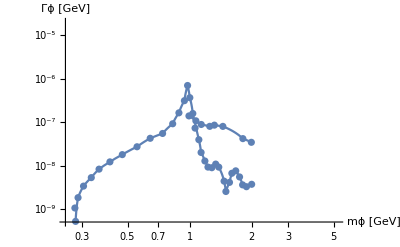

```mathematica
Show[LogLogPlot[{ΓϕKK[mϕ]*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ]},{mϕ,0.25,5.2},PlotRange->{{0.25,5.2},{5*10^(-10),2*10^(-5)}},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],ListPlot[datapointsKK,PlotRange->{5*10^(-10),2*10^(-5)},ScalingFunctions->{"Log","Log"},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],LogLogPlot[Γϕππ[mϕ]*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ],{mϕ,0.25,5.2},PlotRange->{5*10^(-10),2*10^(-5)},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],ListPlot[datapointsππ,PlotRange->{5*10^(-10),2*10^(-5)},ScalingFunctions->{"Log","Log"},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}]]
```

```mathematica
alphaSValues={{1.03,0.49},{1.27,0.40},{1.55,0.34},{2.14,0.28},{3.48,0.23},{6.11,0.19}};
```

```mathematica
AlphaS=Interpolation[alphaSValues,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Γϕχ[mϕ_,mχ_,ξ_,α_]:=1/(8 π mϕ^2) HeavisideTheta[mϕ-2 mχ] ξ^2 Cos[α]^2 (mϕ^2-4 mχ^2)^(3/2) (* dark fermion *)
Γϕf[mϕ_,α_,mf_]:=HeavisideTheta[mϕ-2 mf] ((mf/v)^2 Sin[α]^2 (mϕ^2-4 mf^2)^(3/2))/(8 π mϕ^2) (* lepton *)
ΓϕW[mϕ_,α_]:=HeavisideTheta[mϕ-2 MW] Sin[α]^2 ((EL)^2 (4 (CW)^4 Sqrt[mϕ^2-4 MW^2] (mϕ^4-4 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* W-boson *)
ΓϕZ[mϕ_,α_]:=HeavisideTheta[mϕ-2 MZ] Sin[α]^2 ((EL)^2 (Sqrt[mϕ^2-4 MZ^2] (CW^4 mϕ^4-4 CW^2 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* Z-boson*)
Γϕγ[MH_,α_]:=Sin[α]^2 (EL^6*(MH^4*(3*MH^2-16*MT^2+18*MW^2)^2+256*MT^4*(MH^2-4*MT^2)^2*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^4-72*MH^2*MW^2*(MH^2-2*MW^2)*(3*MH^2-16*MT^2+18*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2+81*MW^4*(17*MH^4-64*MH^2*MW^2+64*MW^4)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^4+32*MT^2*(MH^2-4*MT^2)*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^2*(MH^2*(3*MH^2-16*MT^2+18*MW^2)-36*MW^2*(MH^2-2*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2)))/(18432*MH^5*MW^2*Pi^5*SW^2) (* Photon *)
Γϕg[mϕ_,α_]:=(Sin[α]^2alphas^2mϕ^3)/(32π^3 v^2) Abs[Sum[((mϕ^2/(4mq^2))+((mϕ^2/(4mq^2))-1)*(HeavisideTheta[(mϕ^2/(4mq^2))-1]*(-1/4) (Log[(1+Sqrt[1-1/(mϕ^2/(4mq^2))])/(1-Sqrt[1-1/(mϕ^2/(4mq^2))])]-I π)^2+HeavisideTheta[-(mϕ^2/(4mq^2))+1]ArcSin[Sqrt[(mϕ^2/(4mq^2))]]^2))/((mϕ^2/(4mq^2))^2),{mq,{mu,md,ms,mc,mb,mt}}]]^2*HeavisideTheta[mϕ-2](* gluons *)
Γϕπ[mϕ_,α_]:= Γϕππ[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ] (* pion *)
ΓϕK[mϕ_,α_]:= ΓϕKK[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ] (* kaon *)
Γϕs[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mK] ((ms/v)^2 Sin[α]^2 (mϕ^2-4 mK^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* strange quarks *)
Γϕc[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mD] ((mc/v)^2 Sin[α]^2 (mϕ^2-4 mD^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* charm quarks *)
Γϕb[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mB] ((mb/v)^2 Sin[α]^2 (mϕ^2-4 mB^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* bottom quarks *)
Γϕmoreπs[mϕ_,α_]:=5.1*10^(-9) Sin[α]^2 mϕ^2 Sqrt[mϕ^2-4mπ^2]*HeavisideTheta[mϕ-4mπ]*HeavisideTheta[2-mϕ] (* additional meson contributions *)
Γϕ[mϕ_,mχ_,ξ_,α_]:=(Γϕχ[mϕ,mχ,ξ,α]+Γϕf[mϕ,α,me]+Γϕf[mϕ,α,mμ]+Γϕf[mϕ,α,mτ]+Γϕπ[mϕ,α]+ΓϕK[mϕ,α]+Γϕmoreπs[mϕ,α]+Γϕg[mϕ,α]+Γϕs[mϕ,α]+Γϕc[mϕ,α]+Γϕb[mϕ,α]+Γϕγ[mϕ,α]+ΓϕW[mϕ,α]+ΓϕZ[mϕ,α])/.{alphas:>AlphaS[mϕ]}/.masses/.couplings
ΓϕSM[mϕ_,α_]:=Γϕ[mϕ,mϕ,0,α]
ΓϕBRDM[mϕ_,α_,BRχ_]:=ΓϕSM[mϕ,α](1+BRχ/(1-BRχ))(*ΓSM+Γχ for given BRχ*)
τϕ[mϕ_,mχ_,ξ_,α_]:=10^12(Γϕ[mϕ,mχ,ξ,α] GevToInverseSec)^-1/.constants (*in psc*)
τϕBRDM[mϕ_,α_,BRχ_]:=10^12(ΓϕBRDM[mϕ,α,BRχ] GevToInverseSec)^-1/.constants (*in psc*)
cτϕBRDM[mϕ_,α_,BRχ_]:=3 10^10 10^-12 τϕBRDM[mϕ,α,BRχ](*in cm*)
Γϕtoμμ[mϕ_,α_]:=HeavisideTheta[mϕ-2 mμ] ((mμ/v)^2 Sin[α]^2 (mϕ^2-4 mμ^2)^(3/2))/(8 π mϕ^2)
```

```mathematica
τϕ[1,1,0,0.1]-τϕBRDM[1,0.1,0]
```

0.+0. ⅈ

### Geometrical integration over detector

```mathematica
γβ[γβParent_,mParent_,mϕ_]:=γβParent mParent/(2 mϕ)/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
θminBoost[θmin_,r_,cτ_,γβ_]:=ArcTan[r/(r/Tan[θmin]-γβ cτ)]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
θmaxBoost[θmax_,r_,cτ_,γβ_]:=π+ArcTan[-r/(-r/Tan[θmax]+γβ cτ)]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
GeomInt[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=NIntegrate[Sin[θ]/2(ⅇ^(-dmin/(Sin[θ] γβ  cτ))-ⅇ^(-dmax/(Sin[θ] γβ cτ)))/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{θ,θmin,θmax}]
```

B decays

```mathematica
ΓtotalB=6.582*10^-25/(1.638*10^-12);
```

### Geometry

```mathematica
γβϕB[mϕ_]:=γβ[γβB,mB,mϕ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

### B -> K μμ width

```mathematica
(* The interesting part about the B->Kμμ - process is in the resonance, so that we can take *)
```

```mathematica
ΓBtoKμμ[mϕ_,mχ_,ξ_,α_]:=ΓBtoKϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/Γϕ[mϕ,mχ,ξ,α]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoKϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoXsμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoXsϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoXsππBRDM[mϕ_,α_,BRχ_]:=ΓBtoXsϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKϕ[mϕ_,α_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 fzero[mϕ^2]^2 (mB-mK)^2 (mB+mK)^2 (MB+MS)^2 Sqrt[(mB+mK-mϕ) (mB-mK+mϕ) (mB^2-(mK+mϕ)^2)] (2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)/(4194304 π^5 mB^3 MW^6 SW^6 (MB-MS)^2 (MW^2-MT^2)^6)HeavisideTheta[mB-(mK+mϕ)]
```

```mathematica
ΓBtoXsϕ[mϕ_,α_]:=((Sin[α]mb)/vev (3 √2 GF mt^2 Conjugate[Vts]Vtb)/(15 π^2))^2((mB^2-mϕ^2)^2)/(32 π mB^3)
```

```mathematica
BRBtoKμμBRDMKLM[mϕ_,α_,BRχ_]:=GeomInt[θminBoost[θKLMMin,RKLM,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]],θmaxBoost[θKLMMax,RKLM,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]],0,RKLM,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ΓBtoKμμBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
NoBoostBRBtoKμμBRDMKLM[mϕ_,α_,BRχ_]:=GeomInt[θKLMMin,θKLMMax,0,RKLM,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ΓBtoKμμBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

### B -> K μμ scans

```mathematica
Scanparams={mMin:>0.01,mMax:>10,NMpoints:>30,αMin:>10^-6,αMax:>1,Nαpoints:>30};
```

```mathematica
marr=Range[mMin,mMax,(mMax-mMin)/NMpoints]/.Scanparams//N;
αarr=Range[αMin,αMax,(αMax-αMin)/Nαpoints]/.Scanparams//N;
```

Range::range: Range specification in Range[mMin,mMax,(mMax-mMin)/NMpoints] does not have appropriate bounds.

Range::range: Range specification in Range[αMin,αMax,(αMax-αMin)/Nαpoints] does not have appropriate bounds.

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.38667+0. ⅈ}. NIntegrate obtained 6.08273×10^-15+0. ⅈ and 1.47394×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.0725503521545588998071504160093904077018367636883859848874809074×10^-6}. NIntegrate obtained 9.72825×10^-6+0. ⅈ and 7.81663×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.6790127420752087726609199250125202702091126254342779720745993716×10^-6}. NIntegrate obtained 0.0000154323+0. ⅈ and 2.36542×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

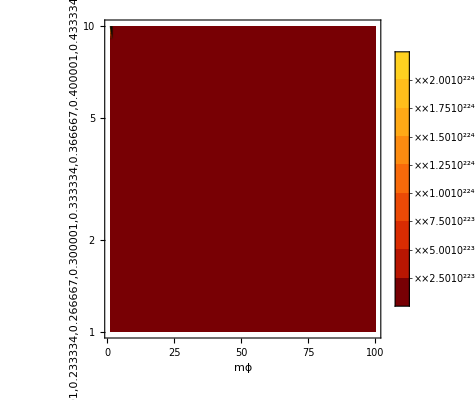

BtoKmumu_BR0.png

```mathematica
BtoKμμBR0=ListContourPlot[Table[Re[BRBtoKμμBRDMKLM[mϕ,α,0]],{mϕ,0.01,5,0.5},{α,10^-6,1,10^-2}],PlotLegends->Automatic,ColorFunction->ColorData["SolarColors"],ContourLabels->True,FrameLabel->{mϕ,α},ScalingFunctions->{None,"Log"},PlotRange->Full]
Export["BtoKmumu_BR0.png",%]
```

```mathematica
BtoKμμBR0=ListContourPlot[Table[Re[BRBtoKμμBRDMKLM[mϕ,α,0]],{mϕ,0.01,3,0.5},{α,10^-6,1,10^-2}],PlotLegends->Automatic,ColorFunction->ColorData["SolarColors"],ContourLabels->True,FrameLabel->{mϕ,α},ScalingFunctions->{None,"Log"},PlotRange->Full]
Export["BtoKmumu_BR0.png",%]
```

```mathematica
Table[{m=marr,α=αarr,Re[BRBtoKμμBRDMKLM[m,α,0]]},{1}]//TableForm
```

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.008} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.341} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::nlim: θ = {-3.87266×10^-15+0. ⅈ,«29»,{0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,«12»,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ,0.698132+0. ⅈ}} is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

$Aborted